# h=√12 QR=1/(√12)(I+C+C^2)(1+D+D^2+D^3)

measure estimation for the paper
“COMPUTATIONAL EXPLORATIONS OF THE THOMPSON GROUP T FOR THE AMENABILITY PROBLEM OF F” 
by S. Haagerup, U. Haagerup, M. Ramirez-Solano:

```mathematica
(*starts with m_0, m_1...*)
```

```mathematica
m0={1/4,1,6,42,318,2528,20790,175344,1508158,13177554,116636378,1043596346,9423929906,85780131568,786252907282,7251162207110,67241091321510,626619942680948,5865627675769158,55130780282172364,520110723876289138,4923701716098043110,46759540919860581346,445382340814268264936,4253954798148920432622,40735421620966779279998,391022235546378412228050,3761992784005490950198026,36271465945557216051920334}
```

{1/4,1,6,42,318,2528,20790,175344,1508158,13177554,116636378,1043596346,9423929906,85780131568,786252907282,7251162207110,67241091321510,626619942680948,5865627675769158,55130780282172364,520110723876289138,4923701716098043110,46759540919860581346,445382340814268264936,4253954798148920432622,40735421620966779279998,391022235546378412228050,3761992784005490950198026,36271465945557216051920334}

```mathematica
Ntuple=Length[m0]-1
```

28

```mathematica
fFree=Function[x,1/(2π)(√(24-(x^2-5)^2))/(x(12-x^2))]
```

Function[x,(√(24-(x^2-5)^2))/((2 π) (x (12-x^2)))]

```mathematica
Clear[mfr]
mfr[0]=1/4
mfr[1]=1
Table[mfr[n]=12mfr[n-1]-6 Total[Table[Binomial[n-2,2j] 6^j 5^(n-2-2j)CatalanNumber[j],{j,0,Floor[(n-2)/2]}]],{n,2,28}];
```

1/4

1

```mathematica
mfree=Table[mfr[k],{k,0,Ntuple}]
```

{1/4,1,6,42,318,2526,20730,174210,1490790,12941430,113658546,1007894922,9010901262,81124563534,734790531306,6690753297042,61209468227190,562304248480230,5184964730621730,47971432345053210,445190135546838558,4143014547695983806,38653861973794352346,361480610332813493922,3387768097335761565318,31813306282794327869526,299300899060093678061970,2820691155247749325150890,26625714096469121592426030}

```mathematica
(*mfree=Table[Integrate[fFree[x] x^(2k),{x,,Sqrt[2]+Sqrt[3]}],{k,0,Ntuple}];*)
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/maria/Dropbox/phd-pd-cs/postdoc/postdoc/ThompsonT/Mathematica

```mathematica
(*DumpSave["density by Legendre polynomials.mx","Global`"]*)
```

{Global`}

```mathematica
(*<<"density by Legendre polynomials.mx"*)
```

```mathematica
(*DumpSave["density by Legendre polynomials.mx","Global`"]*)
```

{Global`}

```mathematica
ChebyshevT[0,x]
ChebyshevT[1,x]
ChebyshevT[2,x]
ChebyshevT[3,x]
ChebyshevT[4,x]
```

1

x

-1+2 x^2

-3 x+4 x^3

1-8 x^2+8 x^4

```mathematica
(*extracting the even coefficients of ChebyshevT[x]*)
```

```mathematica
Table[Reverse[PadLeft[MonomialList[ChebyshevT[k,x^(1/2)]],20+1]],{k,0,40,2}]//MatrixForm
Table[Reverse[PadLeft[MonomialList[ChebyshevT[k,x^(1/2)]],20+1]],{k,0,40,2}]//Dimensions
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 2 x | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | -8 x | 8 x^2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 18 x | -48 x^2 | 32 x^3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | -32 x | 160 x^2 | -256 x^3 | 128 x^4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 50 x | -400 x^2 | 1120 x^3 | -1280 x^4 | 512 x^5 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | -72 x | 840 x^2 | -3584 x^3 | 6912 x^4 | -6144 x^5 | 2048 x^6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 98 x | -1568 x^2 | 9408 x^3 | -26880 x^4 | 39424 x^5 | -28672 x^6 | 8192 x^7 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | -128 x | 2688 x^2 | -21504 x^3 | 84480 x^4 | -180224 x^5 | 212992 x^6 | -131072 x^7 | 32768 x^8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 162 x | -4320 x^2 | 44352 x^3 | -228096 x^4 | 658944 x^5 | -1118208 x^6 | 1105920 x^7 | -589824 x^8 | 131072 x^9 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | -200 x | 6600 x^2 | -84480 x^3 | 549120 x^4 | -2050048 x^5 | 4659200 x^6 | -6553600 x^7 | 5570560 x^8 | -2621440 x^9 | 524288 x^10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 242 x | -9680 x^2 | 151008 x^3 | -1208064 x^4 | 5637632 x^5 | -16400384 x^6 | 30638080 x^7 | -36765696 x^8 | 27394048 x^9 | -11534336 x^10 | 2097152 x^11 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | -288 x | 13728 x^2 | -256256 x^3 | 2471040 x^4 | -14057472 x^5 | 50692096 x^6 | -120324096 x^7 | 190513152 x^8 | -199229440 x^9 | 132120576 x^10 | -50331648 x^11 | 8388608 x^12 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 338 x | -18928 x^2 | 416416 x^3 | -4759040 x^4 | 32361472 x^5 | -141213696 x^6 | 412778496 x^7 | -825556992 x^8 | 1133117440 x^9 | -1049624576 x^10 | 627048448 x^11 | -218103808 x^12 | 33554432 x^13 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | -392 x | 25480 x^2 | -652288 x^3 | 8712704 x^4 | -69701632 x^5 | 361181184 x^6 | -1270087680 x^7 | 3111714816 x^8 | -5369233408 x^9 | 6499598336 x^10 | -5402263552 x^11 | 2936012800 x^12 | -939524096 x^13 | 134217728 x^14 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 450 x | -33600 x^2 | 990080 x^3 | -15275520 x^4 | 141892608 x^5 | -859955200 x^6 | 3572121600 x^7 | -10478223360 x^8 | 22052208640 x^9 | -33426505728 x^10 | 36175872000 x^11 | -27262976000 x^12 | 13589544960 x^13 | -4026531840 x^14 | 536870912 x^15 | 0 | 0 | 0 | 0 | 0
1 | -512 x | 43520 x^2 | -1462272 x^3 | 25798656 x^4 | -275185664 x^5 | 1926299648 x^6 | -9313976320 x^7 | 32133218304 x^8 | -80648077312 x^9 | 148562247680 x^10 | -200655503360 x^11 | 196293427200 x^12 | -135291469824 x^13 | 62277025792 x^14 | -17179869184 x^15 | 2147483648 x^16 | 0 | 0 | 0 | 0
-1 | 578 x | -55488 x^2 | 2108544 x^3 | -42170880 x^4 | 511673344 x^5 | -4093386752 x^6 | 22761029632 x^7 | -91044118528 x^8 | 267776819200 x^9 | -586290298880 x^10 | 959384125440 x^11 | -1167945891840 x^12 | 1042167103488 x^13 | -661693399040 x^14 | 282930970624 x^15 | -73014444032 x^16 | 8589934592 x^17 | 0 | 0 | 0
1 | -648 x | 69768 x^2 | -2976768 x^3 | 66977280 x^4 | -916844544 x^5 | 8307167232 x^6 | -52581629952 x^7 | 240999137280 x^8 | -819082035200 x^9 | 2095125626880 x^10 | -4063273943040 x^11 | 5977134858240 x^12 | -6620826304512 x^13 | 5429778186240 x^14 | -3195455668224 x^15 | 1275605286912 x^16 | -309237645312 x^17 | 34359738368 x^18 | 0 | 0
-1 | 722 x | -86640 x^2 | 4124064 x^3 | -103690752 x^4 | 1589924864 x^5 | -16188325888 x^6 | 115630899200 x^7 | -601280675840 x^8 | 2334383800320 x^9 | -6880289095680 x^10 | 15547666268160 x^11 | -27039419596800 x^12 | 36108024938496 x^13 | -36681168191488 x^14 | 27827093110784 x^15 | -15260018802688 x^16 | 5712306503680 x^17 | -1305670057984 x^18 | 137438953472 x^19 | 0
1 | -800 x | 106400 x^2 | -5617920 x^3 | 156900480 x^4 | -2677768192 x^5 | 30429184000 x^6 | -243433472000 x^7 | 1424085811200 x^8 | -6254808268800 x^9 | 21002987765760 x^10 | -54553214976000 x^11 | 110292369408000 x^12 | -173752901959680 x^13 | 212364657950720 x^14 | -199183403319296 x^15 | 140552804761600 x^16 | -72155450572800 x^17 | 25426206392320 x^18 | -5497558138880 x^19 | 549755813888 x^20)

{21,21}

```mathematica
(*
gamma_k = the dot product of the coefficients of  ChebyshevT[k,x^(1/2)/(1+q)] with the list of moments {m_0,... ,m_k}.
That is, gamma_k = Integral[ChebyshevT[k,x^(1/2)/(1+q)], {-(1+q),1+q}];
 See example below
*)
(*q=1+Sqrt[2]*)
q=2415/1000
gammak=Function[k,
poly=Reverse[MonomialList[ ChebyshevT[k,x^(1/2)/(1+q)]]];
exponentsk=Map[Exponent[#,x]&,poly];
mks=m0⟦1+exponentsk⟧;
mks.poly/.x->1]
```

483/200

Function[k,poly=Reverse[MonomialList[ChebyshevT[k,(√x)/(1+q)]]];exponentsk=(Exponent[#1,x]&)/@poly;mks=m0⟦1+exponentsk⟧;mks.poly/.x→1]

```mathematica
gammak[6]
ChebyshevT[6,x^(1/2)/(1+q)]//Expand
m0⟦{1,2,3,4}⟧
m0⟦{1,2,3,4}⟧.{-1,(720000 x)/466489,-(76800000000 x^2)/217611987121,(2048000000000000 x^3)/101513598260088169}/.x->1
```

9440399848391831/406054393040352676

-1+(720000 x)/466489-(76800000000 x^2)/217611987121+(2048000000000000 x^3)/101513598260088169

{1/4,1,6,42}

9440399848391831/406054393040352676

```mathematica
1+Sqrt[2]//N
```

2.41421

```mathematica
Integrate[1/Sqrt[π] ChebyshevT[0,x] 1/Sqrt[π] ChebyshevT[0,x] 1/Sqrt[1-x^2],{x,-1,1}]
Integrate[Sqrt[2]/Sqrt[π] ChebyshevT[1,x] Sqrt[2]/Sqrt[π] ChebyshevT[1,x] 1/Sqrt[1-x^2],{x,-1,1}]
Integrate[Sqrt[2]/Sqrt[π] ChebyshevT[1,x] Sqrt[2]/Sqrt[π] ChebyshevT[1,x] 1/Sqrt[1-x^2],{x,-1,1}]
(*compare with Legendre *)
Integrate[Sqrt[0+1/2]LegendreP[0,x]Sqrt[0+1/2]LegendreP[0,x],{x,-1,1}]
Integrate[Sqrt[2+1/2]LegendreP[2,x]Sqrt[2+1/2]LegendreP[2,x],{x,-1,1}]
Integrate[Sqrt[3+1/2]LegendreP[3,x]Sqrt[3+1/2]LegendreP[3,x],{x,-1,1}]
```

1

1

1

«3 more identical outputs»

```mathematica
gammak[0]
gammak[2]
gammak[4]
```

1/4

-146489/1865956

-72293932879/870447948484

{1.,-0.0785061,-0.0830537,0.0232491,-0.0136955,0.0433242,-0.0186134,0.0149441,-0.0128543,0.00616308,-0.0141775,0.00224593,0.00672435,0.00234509,-0.00225492,-0.00330586,0.00672082,-0.00438776,0.0000674592,-0.00361309,0.00510266,-0.0022134,0.00214944,-0.00201449,0.00174187,-0.00147809,0.000522668,-0.000386507,0.0000451589}

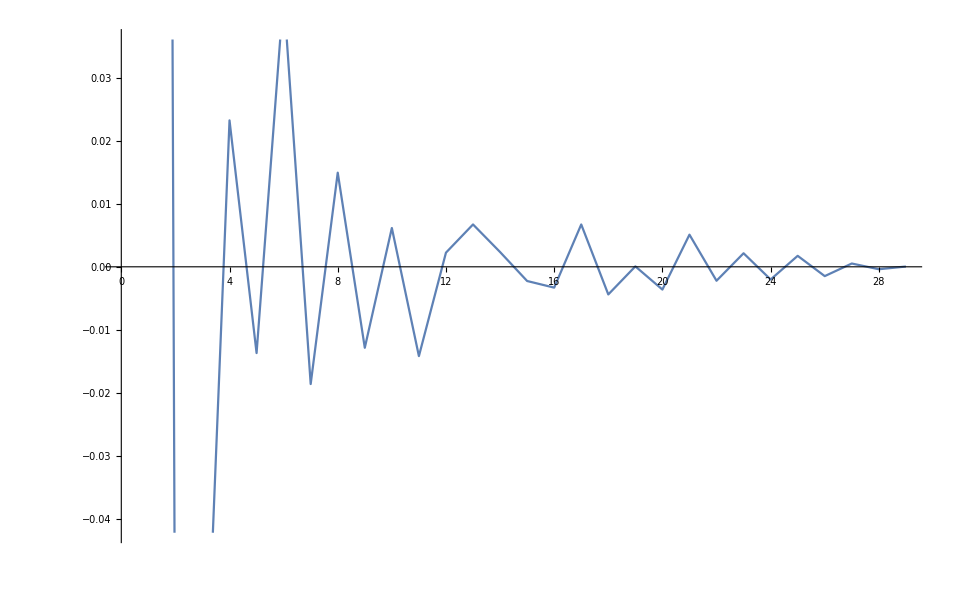

```mathematica
(*plotting the gamma_k. note the oscillations.*)
Prepend[Table[gammak[k],{k,2,2*Ntuple,2}],1];
Prepend[Table[gammak[k],{k,2,2*Ntuple,2}],1]//N
ListPlot[Prepend[Table[gammak[k],{k,2,2*Ntuple,2}],1],Joined->True]
```

```mathematica
(*test*)
Total[Table[gamma[k] T[k],{k,2,2*Ntuple,2}]]
```

gamma[2] T[2]+gamma[4] T[4]+gamma[6] T[6]+gamma[8] T[8]+gamma[10] T[10]+gamma[12] T[12]+gamma[14] T[14]+gamma[16] T[16]+gamma[18] T[18]+gamma[20] T[20]+gamma[22] T[22]+gamma[24] T[24]+gamma[26] T[26]+gamma[28] T[28]+gamma[30] T[30]+gamma[32] T[32]+gamma[34] T[34]+gamma[36] T[36]+gamma[38] T[38]+gamma[40] T[40]+gamma[42] T[42]+gamma[44] T[44]+gamma[46] T[46]+gamma[48] T[48]+gamma[50] T[50]+gamma[52] T[52]+gamma[54] T[54]+gamma[56] T[56]

```mathematica
Clear[f]
f[x_]:=Evaluate[Expand[1*gammak[0]* ChebyshevT[0,x]+2Total[Table[gammak[k] ChebyshevT[k,x],{k,2,2 Ntuple,2}]]]];
f[x]
```

30156861280077133929273563820764673301663453212003856354719719752879488477612507114136130535963017095699443709972181375324314460566810188623687788528064198617/2136089265161900972492414628796562566094065868865216194658506908428459405753553310621344930011138665297949003275980985836985082511853011188394626642282002248324-(14376906851619950657703927631657327509700161701946157164445909332950204648074645656673709179370296230678527876146722310734718626124322293563967647976967216852834 x^2)/534022316290475243123103657199140641523516467216304048664626727107114851438388327655336232502784666324487250818995246459246270627963252797098656660570500562081+(3568203339725549482591978005797065940469747704019494414796804920822024881332148466857127450800982992192278225060662316075051946758434626591063551678157704232879108 x^4)/534022316290475243123103657199140641523516467216304048664626727107114851438388327655336232502784666324487250818995246459246270627963252797098656660570500562081-(232801438903136792213902744302244053384289089179800988438385454100533056428507196906836111732751431646552724308875211593391061689181367580396774560636251282891710576 x^6)/534022316290475243123103657199140641523516467216304048664626727107114851438388327655336232502784666324487250818995246459246270627963252797098656660570500562081+(8364330005876324574976688845794132363328637286143520048554964206201692214652891383050368268822322376466873193626909381109328364707878985852532627814125049843436025600 x^8)/534022316290475243123103657199140641523516467216304048664626727107114851438388327655336232502784666324487250818995246459246270627963252797098656660570500562081-(195969535693455189446832631573874600279316282349771069220309618179390246722290387143684106032833339834669700244561487232573569363942611376512113974264215939709581537280 x^10)/534022316290475243123103657199140641523516467216304048664626727107114851438388327655336232502784666324487250818995246459246270627963252797098656660570500562081+(3245111087257497153002731751786681051100145648798029359006299040342476943553917612593146660356820813089296890763768220250445643650303234933501855733414123945011984752640 x^12)/534022316290475243123103657199140641523516467216304048664626727107114851438388327655336232502784666324487250818995246459246270627963252797098656660570500562081-(39895258714678986343289791101601243414424128262121645877037320988427880125904258697751682739075162499099361497598096672002987109927673207363789718740277011355188196638720 x^14)/534022316290475243123103657199140641523516467216304048664626727107114851438388327655336232502784666324487250818995246459246270627963252797098656660570500562081+(376656378129488686070564231112784199817806419728810151947432567381994019486883487102073193517138499336750300317323050991753926797699557446756596615507891018702276364042240 x^16)/534022316290475243123103657199140641523516467216304048664626727107114851438388327655336232502784666324487250818995246459246270627963252797098656660570500562081-(2799201795754853416301233092079731366437429453240901473291991535127031829369268548767056010657687341903080393180669281115683639132538191366544450789780326443049874338611200 x^18)/534022316290475243123103657199140641523516467216304048664626727107114851438388327655336232502784666324487250818995246459246270627963252797098656660570500562081+(16684074926387669090178774202018713761843849208838896338972905186133219508408586542956352165669698457047741568680919910585888592313591404840643438461387743490707506323783680 x^20)/534022316290475243123103657199140641523516467216304048664626727107114851438388327655336232502784666324487250818995246459246270627963252797098656660570500562081-(80906479472730747775168963816303549145091822446381567366831217345992704067867408332678781257049740938531103646217374378029183084272055740306121753200203941712025755834122240 x^22)/534022316290475243123103657199140641523516467216304048664626727107114851438388327655336232502784666324487250818995246459246270627963252797098656660570500562081+(322757837829540823177781314476410406764052781990589601746988079840436055938037120758723233722006315824401163074425452107748074091686420802997916580431066943802321295783231488 x^24)/534022316290475243123103657199140641523516467216304048664626727107114851438388327655336232502784666324487250818995246459246270627963252797098656660570500562081-(1068137581202265819813433822659055168687822643620815072021743707796039581040472710557828514024936433617467001810320284641310492925385947870195593311510077052955987444976582656 x^26)/534022316290475243123103657199140641523516467216304048664626727107114851438388327655336232502784666324487250818995246459246270627963252797098656660570500562081+(2950556796830228773376132970147064189691764318339557634828623003391680822511577669532980597232656748200308846911527973999178614583345893947424756146996445505747133694486773760 x^28)/534022316290475243123103657199140641523516467216304048664626727107114851438388327655336232502784666324487250818995246459246270627963252797098656660570500562081-(6831445717106377425063269474910811137269422814167629913943291864426484776056834777617463421891529817519720498562363882193091878648447429304294565352260027805947927061600403456 x^30)/534022316290475243123103657199140641523516467216304048664626727107114851438388327655336232502784666324487250818995246459246270627963252797098656660570500562081+(13287848649880412494615260311388755595957936004749736236952609952130185282666346332564834904393593578251591804396873764474952268083742705508931254570179190474152234490672447488 x^32)/534022316290475243123103657199140641523516467216304048664626727107114851438388327655336232502784666324487250818995246459246270627963252797098656660570500562081-(21724233486675462998834355320292899629000305181174506749881313633136850359051769296580646262685453054326510977282013526556573861432883581569866201516223046656638784592970514432 x^34)/534022316290475243123103657199140641523516467216304048664626727107114851438388327655336232502784666324487250818995246459246270627963252797098656660570500562081+(29811430202217114078095121279166369039481744684275310464904393259579001603273002929718975476968410478824815149928155707750303007950138990924403853070709123037155819829774516224 x^36)/534022316290475243123103657199140641523516467216304048664626727107114851438388327655336232502784666324487250818995246459246270627963252797098656660570500562081-(34220084059108291946668135244177340717432050386093118200953871803139339278622111842175664762192734195495733835426520988791786120316519631203545810240600977322508605068578652160 x^38)/534022316290475243123103657199140641523516467216304048664626727107114851438388327655336232502784666324487250818995246459246270627963252797098656660570500562081+(32667785631245118058609198715503585342710838045864524062747211251750312064543795659880582052968884565871358677565916261498459764761042715549510584147204011990089276816235692032 x^40)/534022316290475243123103657199140641523516467216304048664626727107114851438388327655336232502784666324487250818995246459246270627963252797098656660570500562081-(25710534008718204222547932005351985145073548645978563434494512282568041507519427867439337232541874674224719319805151517164603914229929957430635016836063244797597385443975888896 x^42)/534022316290475243123103657199140641523516467216304048664626727107114851438388327655336232502784666324487250818995246459246270627963252797098656660570500562081+(16474406312371242602396382517032724442588913116262673553022297578842213501389588404750910461326053493826003140551514078860432584425640777777171941689466624746835982763195105280 x^44)/534022316290475243123103657199140641523516467216304048664626727107114851438388327655336232502784666324487250818995246459246270627963252797098656660570500562081-(8442245369978289974691974248356334451195564280958305727057004631343229036311877325915189753862312525001266485692325616453336866923797421418069628104948678197225773748254146560 x^46)/534022316290475243123103657199140641523516467216304048664626727107114851438388327655336232502784666324487250818995246459246270627963252797098656660570500562081+(3371556108645967686031735795327054385324319831595940332514742117844647691159010677571342613624052655466517096757349605667657580266176534619954532131803108363612976066016051200 x^48)/534022316290475243123103657199140641523516467216304048664626727107114851438388327655336232502784666324487250818995246459246270627963252797098656660570500562081-(1009298638884163237397892614480948356101864278380199770289724584454152220544040300354713516971104319838782420018798186260252458185976728820562456392304537240065156623737290752 x^50)/534022316290475243123103657199140641523516467216304048664626727107114851438388327655336232502784666324487250818995246459246270627963252797098656660570500562081+(212627863696820214155007966499867924404526780751787735283710178158276147158062275163738885967098926055922383289097188540514535727347922720847508118935031828299154100076937216 x^52)/534022316290475243123103657199140641523516467216304048664626727107114851438388327655336232502784666324487250818995246459246270627963252797098656660570500562081-(28046485214536976790229681625730819260048679345619668616243652676177746248955613460399990673917223375093952571973732625783219205504821067568966133742483309499119597919404032 x^54)/534022316290475243123103657199140641523516467216304048664626727107114851438388327655336232502784666324487250818995246459246270627963252797098656660570500562081+(1737732117197028541913881708591801792092212017752377098274788754653205119860621926132633386949946088918393725725781719369531163747900331538773760484250135183001525319368704 x^56)/534022316290475243123103657199140641523516467216304048664626727107114851438388327655336232502784666324487250818995246459246270627963252797098656660570500562081

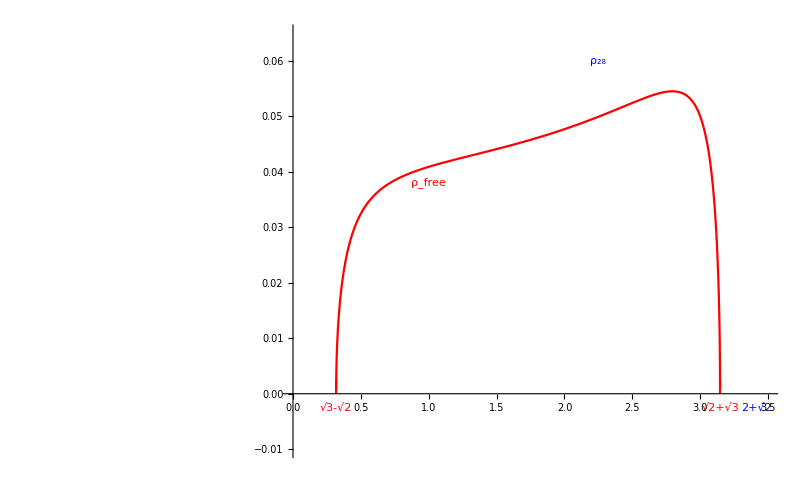

```mathematica
freeGraph=Show[Plot[{1/(2π)(√(24-(x^2-5)^2))/(Abs[x](12-x^2))/.x->t},{t,-3.15,3.15},PlotRange->{{0,3.5},{-.01,.065}},PlotStyle->{Red}],
Graphics[{Red,Style[Text[Subscript[ρ, free],{1,.038}],Large]}],
Graphics[{Blue,Style[Text[Subscript[ρ, 28],{2.25,.06}],Large]}],
ListPlot[{{3.1462643699419726,0},{3.1462643699419726,0.0025}},Joined->True,PlotStyle->Red],
ListPlot[{{0.31783724519578205,0},{0.31783724519578205,0.0025}},Joined->True,PlotStyle->Red],
ListPlot[{{-0.31783724519578205,0},{-0.31783724519578205,0.0025}},Joined->True,PlotStyle->Red],
ListPlot[{{-3.1462643699419726,0},{-3.1462643699419726,0.0025}},Joined->True,PlotStyle->Red],
Graphics[{Blue,Style[Text[2+Sqrt[2],{2+Sqrt[2],-.0025}],Bold,Medium]}],
Graphics[{Red,Style[Text[Sqrt[2]+Sqrt[3],{Sqrt[2]+Sqrt[3]-.0,-.0025}],Bold,Medium]}],
Graphics[{Red,Style[Text[-Sqrt[2]+Sqrt[3],{-Sqrt[2]+Sqrt[3]+.0,-.0025}],Bold,Medium]}],
Graphics[{Red,Style[Text[-Sqrt[2]-Sqrt[3],{-Sqrt[2]-Sqrt[3]+.1,-.0025}],Bold,Medium]}]
]
```

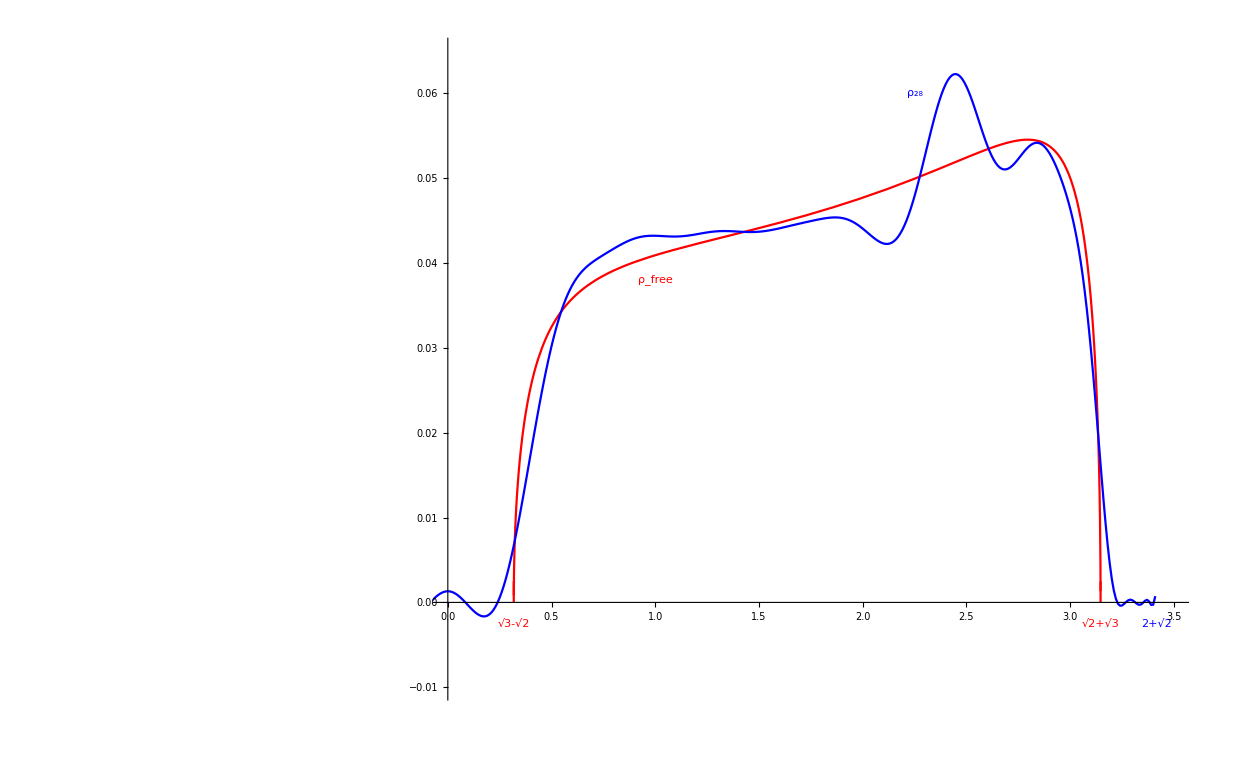

```mathematica
Show[freeGraph,ListPlot[Table[{t,1/π f[t/(1+q)]/(√((1+q)^2-t^2))},{t,-(342/100)+1/100,(342/100)-1/100,1/100}],Joined->True,PlotLabel->"ChebyshevT ONB",PlotStyle->{Blue},PlotRange->{{-3.45,3.45},{-.01,.25}}]]
```

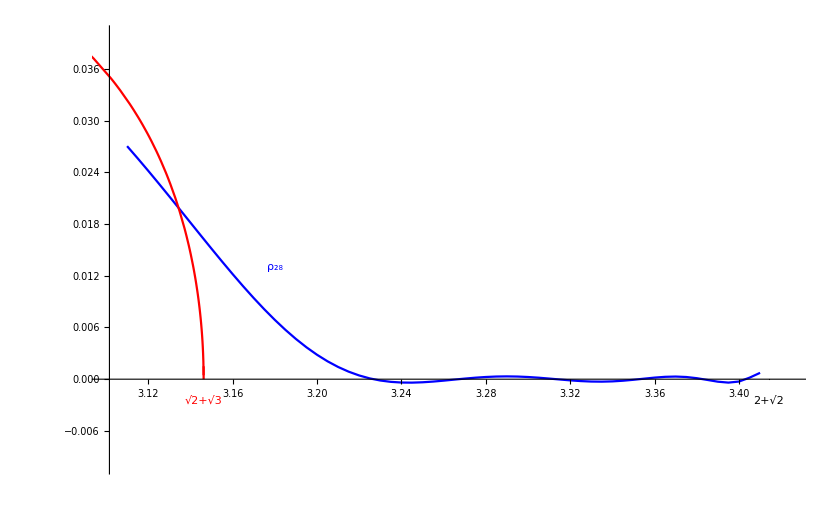

```mathematica
Show[ListPlot[Table[{t,1/π f[t/(1+q)]/(√((1+q)^2-t^2))},{t,(310/100)+1/100,(342/100)-1/100,1/200}],Joined->True,PlotRange->{{3.1,3.425},{-.01,.04}},PlotStyle->Blue],Plot[{1/(2π)(√(24-(x^2-5)^2))/(Abs[x](12-x^2))/.x->t},{t,3,3.42},PlotRange->{{-3.42,3.41},{-1,1}},PlotStyle->Red],
Graphics[{Blue,Style[Text[Subscript[ρ, 28],{3.18,.013}],Large]}],
Graphics[{Red,Style[Text[Sqrt[2]+Sqrt[3],{Sqrt[2]+Sqrt[3],-.0025}],Bold,Medium]}],
ListPlot[{{3.1462643699419726,0},{3.1462643699419726,.0015}},Joined->True,PlotStyle->Red],
Graphics[{Darker[Black],Style[Text[2+Sqrt[2],{2+Sqrt[2],-.0025}],Bold,Medium]}],
Graphics[{Darker[Black],PointSize[.001],Point[{2+Sqrt[2],0}]}]
]
```

```mathematica
NIntegrate[1/(2π)(√(24-(x^2-5)^2))/(Abs[x](12-x^2)),{x,Sqrt[3]-Sqrt[2],Sqrt[3]+Sqrt[2]}]
```

0.125+2.06962×10^-26 ⅈ